Plot a line integral around a parallelopiped path

```mathematica
<<peeters` ;
<<MaTeX`

SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 14]
peeters`setGitDir[ "../project/figures/classicalmechanics" ]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor,txfonts},\definecolor{BlueDarker}{HTML}{0000AA},\definecolor{RedDarker}{HTML}{AA0000},\definecolor{PurpleDarker}{HTML}{550055},\definecolor{OrangeDarker}{HTML}{AA5500},\definecolor{GreenDarker}{HTML}{00AA00}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→14,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

\\wsl$\Ubuntu\home\pjoot\project\figures\classicalmechanics

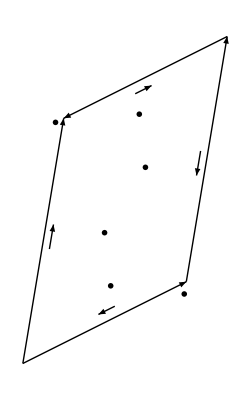

```mathematica
ClearAll[o,a,b]
o ={0,0};
a = {1,0.5};
b = {0.25,1.5};
e = 0.1;

p = Graphics[{
Thick,
Arrow[{o,a}],
Arrow[{o,b}],
Arrow[{a,a+b}],
Arrow[{a + b,b}],

Arrow[{(1+e)a/2 +(e/2) b, (1-e)a/2 + (e/2) b}],
Arrow[{(1-e)a/2 +(1- e/2) b, (1+e)a/2 +(1- e/2) b}],
Arrow[{(1-e)b/2 +(e/2) a, (1+e)b/2 + (e/2) a}],
Arrow[{(1+e)b/2 +(1- e/2) a, (1-e)b/2 +(1- e/2) a}],

Text[ MaTeX["a"], a - (e/2) b],
Text[ MaTeX["b"], b - (e/2) a],

Text[ MaTeX["F(u,1) (+a du) G(u,1)"], a/2 +(1- 1.5e) b],
Text[ MaTeX["F(u,0) (-a du) G(u,0)"], a/2 +(0+ 1.5e) b],

Text[ MaTeX["F(1,v) (-b dv) G(1,v)"], b(e + 1/2) +(1- 4e) a],
Text[ MaTeX["F(0,v) (+b dv) G(0,v)"], b(-e + 1/2) +(0+ 4e) a]

}]
```

```mathematica
peeters`exportForLatex["lineIntegralAroundParallelopipedFig1", p]
```

{lineIntegralAroundParallelopipedFig1.eps,lineIntegralAroundParallelopipedFig1pn.png}